```mathematica
h=10
g=1
s=1
n=4
W= B >= (n-1)(h-R *g)s+h*s
RC = R >= B/(s *g)
```

10

1

1

4

B≥10+3 (10-R)

R≥B

```mathematica
R≥B
```

R≥B

```mathematica
{5,40}
```

{5,40}

```mathematica
D1 =5
L1=12
D2=10
L2=1.5
T1 = {D1*Min[1,L1/(s g)],D1*L1}
T2 = {D2*Min[1,L2/(s g)],D2*L2}
ST ={FontFamily->"Latin Modern Roman 12",18,GrayLevel[0]}
OFF = {2,0}
```

5

12

10

1.5

{5,60}

{10,15.}

{FontFamily→Latin Modern Roman 12,18,GrayLevel[0]}

{2,0}

{2,0}

```mathematica
OR = {0,0}
RE = {25, 25*s*g}
BR = {25,0}
TL = {0,100}
TR = {25,100}
INT = {h/g ,h s}
LE = {0,n h s}
```

{0,0}

{25,25}

{25,0}

{0,100}

{25,100}

{10,10}

{0,40}

```mathematica
{25,0}
ColorData[97,"ColorList"]
```

{25,0}

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

```mathematica
FC=ColorData[97,"ColorList"][[4]]
VC=ColorData[97,"ColorList"][[1]]
```

RGBColor[0.922526, 0.385626, 0.209179]

RGBColor[0.368417, 0.506779, 0.709798]

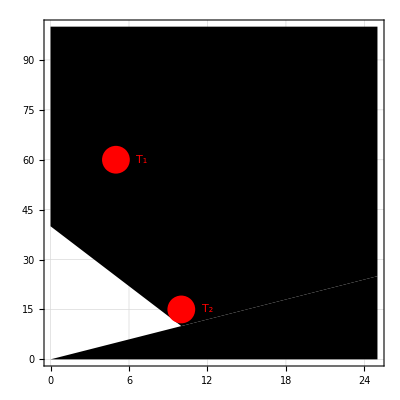

```mathematica
P = RegionPlot[False,{R,0,25},{B,0,100}, GridLines->Automatic,Epilog->{Style[Polygon[{TL,LE,INT,RE,TR}], {Opacity[0.4,VC], EdgeForm[{VC, Thick}]}],Style[Polygon[{OR,RE,BR}], {Opacity[0.4,FC], EdgeForm[{FC, Thick}]}],PointSize[0.05],Red,Point[T1],Point[T2],Style[{Text[Subscript["T","1"], T1 + OFF],Text[Subscript["T","2"], T2 + OFF]},ST]}]
```

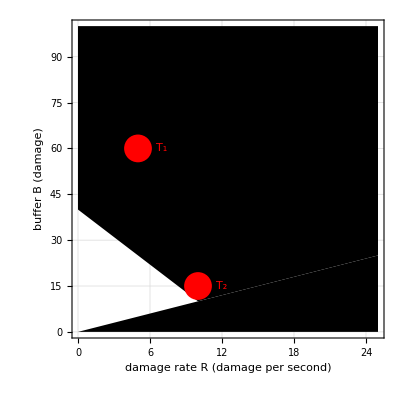

```mathematica
P2 =Show[P,FrameLabel->{{HoldForm[buffer B "(damage)"],None},{HoldForm[damage rate R "(damage per second)"],None}},PlotLabel->None,LabelStyle->ST,PlotRangePadding->0]
```